```mathematica
Solve[{0==-x-a*w*(x^2+w^2-1),0==w},{x,w}]
```

{{x→0,w→0}}

```mathematica
(*Linearize around (0,0)*)
```

```mathematica
-x-a*w*(x^2+w^2-1)/.{x->ex,w->ew}
```

-ex-a ew (-1+ew^2+ex^2)

```mathematica
Eigensystem[{{0,1},{-1,a}}]
```

{{1/2 (a-√(-4+a^2)),1/2 (a+√(-4+a^2))},{{1/2 (a+√(-4+a^2)),1},{1/2 (a-√(-4+a^2)),1}}}

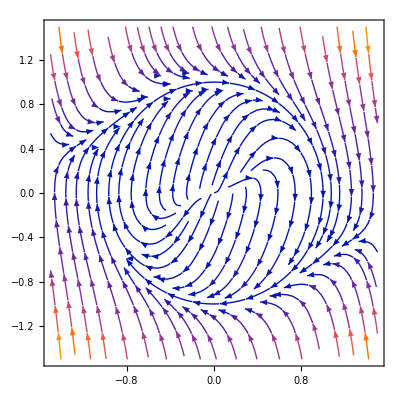

```mathematica
StreamPlot[{w,-x-(3)*w*(x^2+w^2-1)},{x,-1.5,1.5},{w,-1.5,1.5}]
```

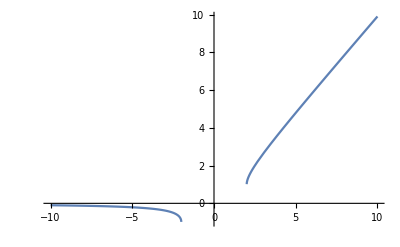

```mathematica
Plot[(a+Sqrt[a^2-4])/2,{a,-10,10},PlotRange->Full]
```

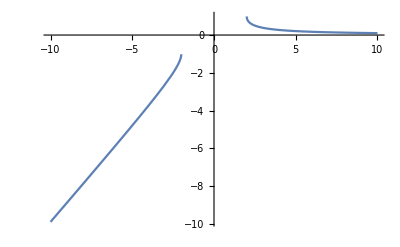

```mathematica
Plot[(a-Sqrt[a^2-4])/2,{a,-10,10},PlotRange->Full]
```